## how accurate is my blackman pulse add sidebands add effect of time dependent light shift.

```mathematica
Clear["Global`*"];
kHz=10^3;nm=10^-9;mK=10^-3;uK=10^-6;us=10^-6;
um=10^-6;
kB=1.38064852 10^-23;ℏ=1.0545718 10^-34;amu=1.66054 10^-27;
mCs=132.90545 amu;mNa = 23amu;
a0= 5.2917721067 10^-11;
ϵ0=8.854187817 10^-12;
c=299792458;
cm=10^-2;
ms=10^-3;
ωrCs=2π 150kHz;
ωaCs=2π 25kHz;
ωrNa=2π 150kHz;
ωaNa=2π 25kHz;
μ=(mNa mCs)/(mCs+mNa);
```

```mathematica
Clear[δ,ρ0]
(*basis: 
1 |n1,Down>
2 |n1,Up>
3 |n2,Down>
4 |n2,Up>
*)
ωtr=ωrCs;
cn1=1; (*start all in spin down*)

ρ0=SparseArray[{{2,2}}->{Abs[cn1]^2}];
Hdet=1/2 δ DiagonalMatrix[{1,-1}];
HR=Ω0/2 SparseArray[{{1,2},{2,1}}->{1,1}];
Hint=DiagonalMatrix[{0,Δ}];

Htot=HR+Hint+Hdet;

Htot//MatrixForm
```

(δ/2 | Ω0/2
Ω0/2 | -δ/2+Δ)

```mathematica
f[ρ0_,δ0_,Ω00_]:=Block[{δ=δ0,ρ=ρ0,Ω0=Ω00},-I (Htot.ρ-ρ.Htot)];

Δ=2π  0 kHz;

Δt=1. us;
(*blackman rabi flop*)
Clear[tEnd,tRaman,square,blackman]
square[t_,tEnd_]:=(HeavisideTheta[t]-HeavisideTheta[t-tEnd]);
blackman[t_,tEnd_]:=√(square[t,tEnd](-1/2 Cos[2π t/tEnd]+2/25 Cos[4π t/tEnd]+21/50));


Clear[δ,Ω0,tEnd]
δ=Δ;
Ω0=2π 1/(2 30us);
T= 1.71 60us;

sim=Reap[Do[
ρ1=ρ0;
Do[
(*Sow[{i Δt/us,ρ1[[1,1]]}];*)

k1=Δt f[ρ1,δ,Ω0 blackman[i Δt,tEnd]];
k2=Δt f[ρ1+k1/2,δ,Ω0 blackman[i Δt,tEnd]];
k3=Δt f[ρ1+k2/2,δ,Ω0 blackman[i Δt,tEnd]];
k4=Δt f[ρ1+k3,δ,Ω0 blackman[i Δt,tEnd]];
ρ1=ρ1+1/3(k1/2+k2+k3+k4/2)
,
{i,0,Ceiling[tEnd/Δt]}
]
Sow[{tEnd/us,ρ1[[1,1]]}],
{tEnd,1us,T,10us}
]][[2,1]];
```

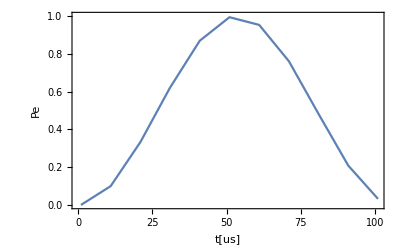

square π-time[us] | blackman π-time[us] | sqrt blackman π-time[us]
30. | 71.4286 | 51.3

```mathematica
ListPlot[Chop[sim],Joined->True,PlotRange->{All,{0,1}},Axes->False,Frame->True,FrameLabel->{"t[us]","Pe"},LabelStyle->{Black,17}]
{{"square π-time[us]","blackman π-time[us]","sqrt blackman π-time[us]"},{2π/Ω0/us/2.,50./21 2π/Ω0/us/2,1.71 2π/Ω0/us/2}}//TableForm
```

```mathematica
(*blackman spectrum*)

Clear[δ,Ω0,T,tEnd]
Ω0=2π 1/(2 30us);
tEnd=1.71 30us 1.;

sim=Reap[Do[
ρ1=ρ0;
Do[
(*Sow[{i Δt/us,ρ1[[1,1]]}];*)

k1=Δt f[ρ1,δ,Ω0 blackman[i Δt,tEnd]];
k2=Δt f[ρ1+k1/2,δ,Ω0 blackman[i Δt,tEnd]];
k3=Δt f[ρ1+k2/2,δ,Ω0 blackman[i Δt,tEnd]];
k4=Δt f[ρ1+k3,δ,Ω0 blackman[i Δt,tEnd]];
ρ1=ρ1+1/3(k1/2+k2+k3+k4/2)
,
{i,0,Ceiling[tEnd/Δt]}
]
Sow[{δ/(2π kHz),ρ1[[1,1]]}],
{δ,Δ-2π 50kHz,Δ+2π 50kHz,2π 3 kHz}
]][[2,1]];
```

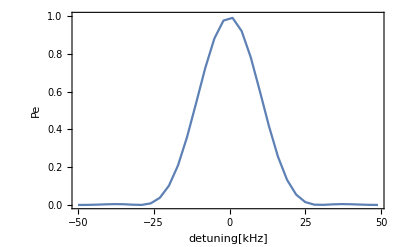

square π-time[us] | blackman π-time[us] | sqrt blackman π-time[us] | pulse time[us]
30. | 71.4286 | 51.3 | 51.3

```mathematica
ListPlot[Chop[sim],Joined->True,PlotRange->{All,{0,1}},Axes->False,Frame->True,FrameLabel->{"detuning[kHz]","Pe"},LabelStyle->{Black,17}]
{{"square π-time[us]","blackman π-time[us]","sqrt blackman π-time[us]","pulse time[us]"},{2π/Ω0/us/2.,50./21 2π/Ω0/us/2,1.71 2π/Ω0/us/2,tEnd/us}}//TableForm
```

```mathematica
(*blackman spectrum, with time varying lightshift*)
Clear[tEnd,tRaman]

Clear[δ,Ω0,T,tEnd]
Ω0=2π 1/(2 30us);
tEnd=1.71 30us 1.;
ϵ=-5Ω0;
sim=Reap[Do[
ρ1=ρ0;
Do[
(*Sow[{i Δt/us,ρ1[[1,1]]}];*)

k1=Δt f[ρ1,δ+ ϵ blackman[i Δt,tEnd],Ω0 blackman[i Δt,tEnd]];
k2=Δt f[ρ1+k1/2,δ +ϵ blackman[i Δt,tEnd],Ω0 blackman[i Δt,tEnd]];
k3=Δt f[ρ1+k2/2,δ +ϵ blackman[i Δt,tEnd],Ω0 blackman[i Δt,tEnd]];
k4=Δt f[ρ1+k3,δ +ϵ blackman[i Δt,tEnd],Ω0 blackman[i Δt,tEnd]];
ρ1=ρ1+1/3(k1/2+k2+k3+k4/2)
,
{i,0,Ceiling[tEnd/Δt]}
]
Sow[{δ/(2π kHz),ρ1[[1,1]]}],
{δ,Δ+2π -20kHz,Δ+2π 150kHz,2π 5 kHz}
]][[2,1]];
```

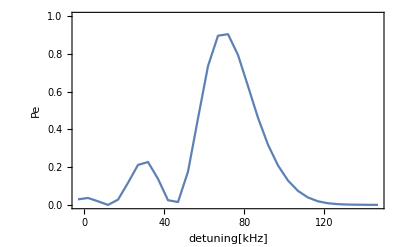

square π-time[us] | blackman π-time[us] | sqrt blackman π-time[us] | pulse time[us]
30. | 71.4286 | 51.3 | 51.3

```mathematica
ListPlot[Chop[sim],Joined->True,PlotRange->{All,{0,1}},Axes->False,Frame->True,FrameLabel->{"detuning[kHz]","Pe"},LabelStyle->{Black,17}]
{{"square π-time[us]","blackman π-time[us]","sqrt blackman π-time[us]","pulse time[us]"},{2π/Ω0/us/2.,50./21 2π/Ω0/us/2,1.71 2π/Ω0/us/2,tEnd/us}}//TableForm
```

```mathematica
(*blackman rabi flop, with time varying lightshift*)
Clear[tEnd,tRaman]

Clear[δ,Ω0,T,tEnd]
Ω0=2π 1/(2 30us);
T=3 1.71 30us ;
δ=69.39kHz 2π;
ϵ=-5Ω0;
sim=Reap[Do[
ρ1=ρ0;
Do[
(*Sow[{i Δt/us,ρ1[[1,1]]}];*)

k1=Δt f[ρ1,δ+ ϵ blackman[i Δt,tEnd],Ω0 blackman[i Δt,tEnd]];
k2=Δt f[ρ1+k1/2,δ +ϵ blackman[i Δt,tEnd],Ω0 blackman[i Δt,tEnd]];
k3=Δt f[ρ1+k2/2,δ +ϵ blackman[i Δt,tEnd],Ω0 blackman[i Δt,tEnd]];
k4=Δt f[ρ1+k3,δ +ϵ blackman[i Δt,tEnd],Ω0 blackman[i Δt,tEnd]];
ρ1=ρ1+1/3(k1/2+k2+k3+k4/2)
,
{i,0,Ceiling[tEnd/Δt]}
]
Sow[{tEnd/us,ρ1[[1,1]]}],
{tEnd,1us,T,10us}
]][[2,1]];
```

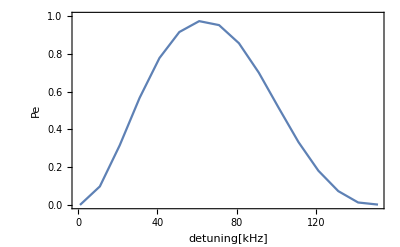

square π-time[us] | blackman π-time[us] | sqrt blackman π-time[us] | pulse time[us]
30. | 71.4286 | 51.3 | 1000000 tEnd

```mathematica
ListPlot[Chop[sim],Joined->True,PlotRange->{All,{0,1}},Axes->False,Frame->True,FrameLabel->{"detuning[kHz]","Pe"},LabelStyle->{Black,17}]
{{"square π-time[us]","blackman π-time[us]","sqrt blackman π-time[us]","pulse time[us]"},{2π/Ω0/us/2.,50./21 2π/Ω0/us/2,1.71 2π/Ω0/us/2,tEnd/us}}//TableForm
```

# square pulse

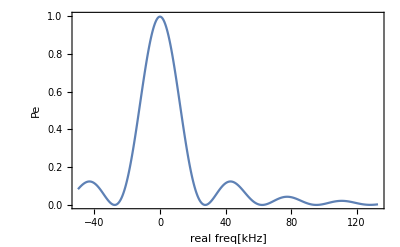

Ω0/2πkHz | Δ/2πkHz | t/us
16.6667 | 0 | 30

```mathematica
(*take square spectrum*)
Clear[δ,Ω0,tEnd]
Ω0=2π 1/(60us) 1.;
tEnd=30us;
sim=Reap[
Do[
ρ1=ρ0;
Do[
k1=Δt f[ρ1,δ,Ω0];
k2=Δt f[ρ1+k1/2,δ,Ω0];
k3=Δt f[ρ1+k2/2,δ,Ω0];
k4=Δt f[ρ1+k3,δ,Ω0];
ρ1=ρ1+1/3(k1/2+k2+k3+k4/2),
{i,0,Ceiling[tEnd/Δt]}
]
Sow[{δ/(2π kHz),ρ1[[1,1]]}]
,{δ,-2π 50kHz,2π 133kHz,2π .3kHz}
]
][[2,1]];

ListPlot[Chop[sim],Joined->True,PlotRange->{All,{0,1}},Axes->False,Frame->True,FrameLabel->{"real freq[kHz]","Pe"},LabelStyle->{Black,17}]
{{"Ω0/2πkHz","Δ/2πkHz","t/us"},{Ω0/(2π kHz),Δ/(2π kHz),tEnd/us}}//TableForm
```

# backup

```mathematica
Clear["Global`*"];
kHz=10^3;nm=10^-9;mK=10^-3;uK=10^-6;us=10^-6;
um=10^-6;
kB=1.38064852 10^-23;ℏ=1.0545718 10^-34;amu=1.66054 10^-27;
mCs=132.90545 amu;mNa = 23amu;
a0= 5.2917721067 10^-11;
ϵ0=8.854187817 10^-12;
c=299792458;
cm=10^-2;
ms=10^-3;
ωrCs=2π 150kHz;
ωaCs=2π 25kHz;
ωrNa=2π 150kHz;
ωaNa=2π 25kHz;
μ=(mNa mCs)/(mCs+mNa);
```

```mathematica
Clear[δ,ρ0]
(*basis: 
1 |n1,Down>
2 |n1,Up>
3 |n2,Down>
4 |n2,Up>
*)
ωtr=ωrCs;
cn1=1; (*start all in spin down*)

ρ0=SparseArray[{{2,2}}->{Abs[cn1]^2}];
Hdet=1/2 δ DiagonalMatrix[{1,-1}];
HR=Ω0/2 SparseArray[{{1,2},{2,1}}->{1,1}];
Hint=DiagonalMatrix[{0,Δ}];

Htot=HR+Hint+Hdet;

Htot//MatrixForm
```

(δ/2 | Ω0/2
Ω0/2 | -δ/2+Δ)

```mathematica
f[ρ0_,δ0_,Ω00_]:=Block[{δ=δ0,ρ=ρ0,Ω0=Ω00},-I (Htot.ρ-ρ.Htot)];

Δ=2π 28.3kHz;

Δt=1us;
tEnd=30us;
```

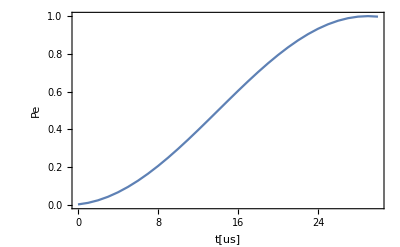

Ω0/2πkHz | Δ/2πkHz | t/us
50/3 | 28.3 | 30

```mathematica
(*rabi flop*)
Clear[δ,Ω0]
δ=Δ;
Ω0=2π 1/(60us);
sim=Reap[
ρ1=ρ0;
Do[
k1=Δt f[ρ1,δ,Ω0];
k2=Δt f[ρ1+k1/2,δ,Ω0];
k3=Δt f[ρ1+k2/2,δ,Ω0];
k4=Δt f[ρ1+k3,δ,Ω0];
ρ1=ρ1+1/3(k1/2+k2+k3+k4/2);
Sow[{i Δt/us,ρ1[[1,1]]}]
,
{i,0,Ceiling[tEnd/Δt]}
]

][[2,1]];

ListPlot[Chop[sim],Joined->True,PlotRange->{All,{0,1}},Axes->False,Frame->True,FrameLabel->{"t[us]","Pe"},LabelStyle->{Black,17}]
{{"Ω0/2πkHz","Δ/2πkHz","t/us"},{Ω0/(2π kHz),Δ/(2π kHz),tEnd/us}}//TableForm
```

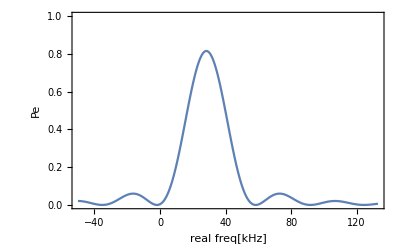

Ω0/2πkHz | Δ/2πkHz | t/us
11.57 | 28.3 | 30

```mathematica
(*take spectrum*)
Clear[δ,Ω0]
Ω0=2π 1/(60us);
sim=Reap[
Do[
ρ1=ρ0;
Do[
k1=Δt f[ρ1,δ,Ω0];
k2=Δt f[ρ1+k1/2,δ,Ω0];
k3=Δt f[ρ1+k2/2,δ,Ω0];
k4=Δt f[ρ1+k3,δ,Ω0];
ρ1=ρ1+1/3(k1/2+k2+k3+k4/2),
{i,0,Ceiling[tEnd/Δt]}
]
Sow[{δ/(2π kHz),ρ1[[1,1]]}]
,{δ,-2π 50kHz,2π 133kHz,2π .3kHz}
]
][[2,1]];

ListPlot[Chop[sim],Joined->True,PlotRange->{All,{0,1}},Axes->False,Frame->True,FrameLabel->{"real freq[kHz]","Pe"},LabelStyle->{Black,17}]
{{"Ω0/2πkHz","Δ/2πkHz","t/us"},{Ω0/(2π kHz),Δ/(2π kHz),tEnd/us}}//TableForm
```